```mathematica
SetDirectory["/Users/wenqiangfang/Dropbox (Personal)/WenqiangMaxHaneesh/ClausenPostbucklingandSensitivity/"]
```

/Users/wenqiangfang/Dropbox (Personal)/WenqiangMaxHaneesh/ClausenPostbucklingandSensitivity

```mathematica
Import["Sensitivity_constant_TEST.mat","Labels"]
```

{N,Nb,norm_r1,beta,rhat,d,Psi}

constant p1

```mathematica
data2 = Import["/Users/wenqiangfang/Dropbox (Personal)/WenqiangMaxHaneesh/ClausenPostbucklingandSensitivity/Sensitivity_constant_TEST.mat",{"Data",{6,7}}];
```

```mathematica
data2//Dimensions
```

{2,1000000,1}

```mathematica
d=Flatten@data2[[1]];
```

```mathematica
Psi = Flatten@data2[[2]];
```

```mathematica
d//Length
```

1000000

```mathematica
ConData=Partition[Riffle[d,Psi],2];
```

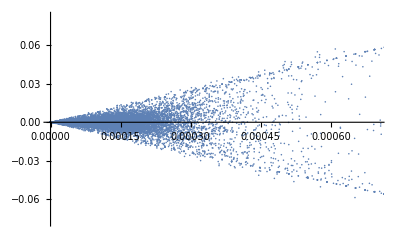

```mathematica
p1=ListPlot[ConData[[;;;;50]],PlotRange->{{0,0.0007},All}]
```

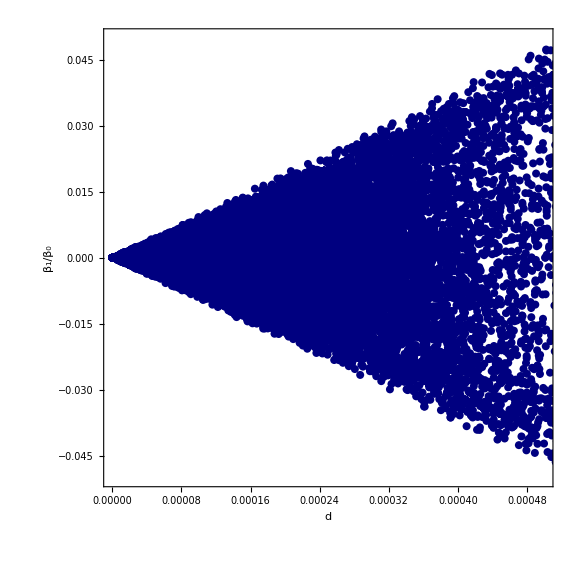

```mathematica
p1=ListPlot[ConData[[1;;300000;;10]],
PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0,0,0.5],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
AxesStyle->Directive[Black,FontFamily->"Times",24],
Frame->True,
FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False]
```

```mathematica
2Sqrt[6 ]/0.05
```

97.9796

```mathematica
pcons=Plot[{-97.97958971132712x,97.97958971132712x},{x,0,0007},PlotStyle->Directive[{RGBColor[0,0,1],Thickness[0.008]}]];
```

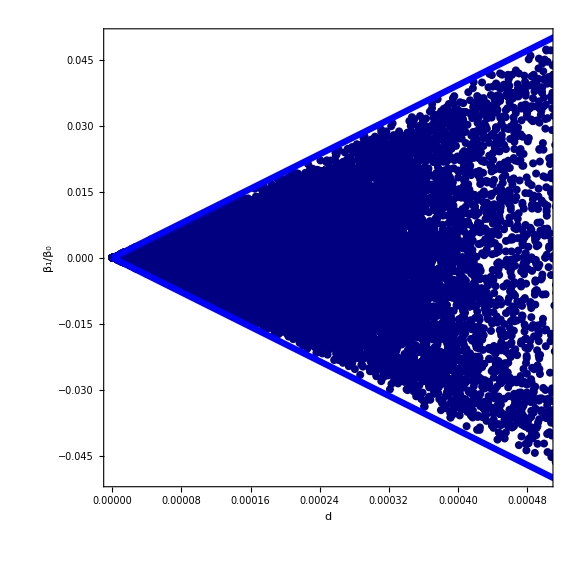

```mathematica
PConstant=Show[p1,pcons]
```

```mathematica
Export["PConstant_v3.eps",PConstant]
```

PConstant_v3.eps

```mathematica
w
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Study/ASME2018/Figure

```mathematica
Export["PtsConst_v1.eps",p1]
```

PtsConst_v1.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PtsClausen_v1.eps"]]]
```

constant p4

```mathematica
Import["Sensitivity_constant_Nb_1_50.mat","Labels"]
```

{Psi,beta,d,norm_r1,rhat}

```mathematica
data2 = Import["Sensitivity_constant_Nb_1_50.mat",{"Data",{3,1}}];
```

{2,4000000,1}

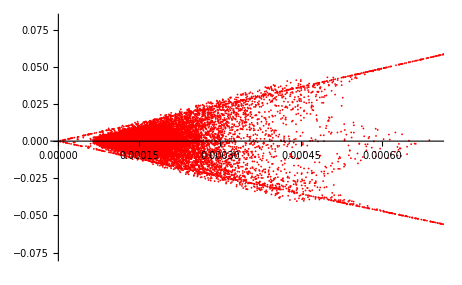

```mathematica
data2 = Import["Sensitivity_constant_Nb_1_50.mat",{"Data",{3,1}}];
data2//Dimensions
d=Flatten@data2[[1]];
Psi = Flatten@data2[[2]];
ConData4=Partition[Riffle[d,Psi],2];
p4=ListPlot[ConData4[[;;;;100]],PlotRange->{{0,0.0007},All},PlotStyle->Red]
```

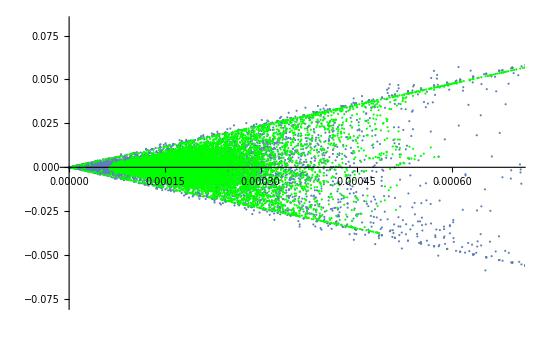

```mathematica
Show[p1,p3]
```

Clausen p2

```mathematica
Import["Sensitivity_clausen_TEST.mat","Labels"]
```

{N,Nb,norm_r1,beta,rhat,d,Psi}

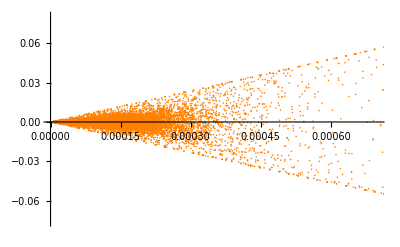

```mathematica
data2 = Import["Sensitivity_clausen_TEST.mat",{"Data",{6,7}}];
d=Flatten@data2[[1]];
Psi = Flatten@data2[[2]];
ConData2=Partition[Riffle[d,Psi],2];
p2=ListPlot[ConData2[[;;;;50]],PlotRange->{{0,0.0007},All},PlotStyle->Orange]
```

```mathematica
pcons=Plot[{-97.980x,97.980x},{x,0,0005},PlotStyle->Red];
```

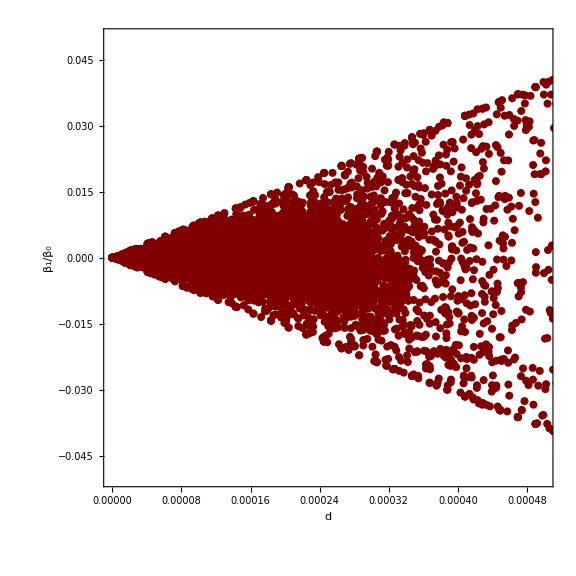

```mathematica
p2=ListPlot[ConData2[[Range[1,1000000,50]]],
PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0.5,0,0],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
AxesStyle->Directive[Black,FontFamily->"Times",24],
Frame->True,
FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Study/ASME2018/Figure

```mathematica
Export["PtsClausen_v3.eps",p2]
```

PtsClausen_v3.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PtsClausen_v3.eps"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PtsClausen_v1.eps"]]]
```

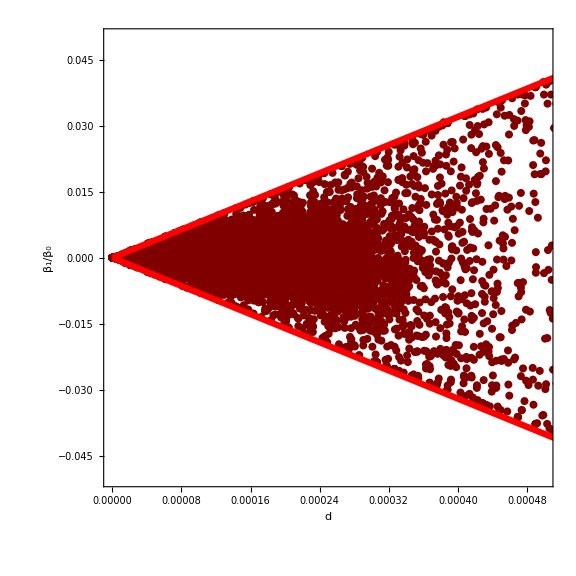

```mathematica
pclau=Plot[{-80x,80x},{x,0,0005},PlotStyle->Directive[{RGBColor[1,0,0],Thickness[0.008]}]];
PClausen=Show[p2,pclau]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Study/ASME2018/Figure

```mathematica
Export["PClausen_v3.eps",PClausen]
```

PClausen_v3.eps

```mathematica
SystemOpen["PClausen_v1.eps"]
```

```mathematica
Show[p1,p2,pclau,pcons,ImageSize->Large,AspectRatio->Full]
```

```mathematica
N@(1-Sqrt[2/3])
```

0.183503

```mathematica
(97.980-80)/97.980//N
```

0.183507

```mathematica
Quit
```

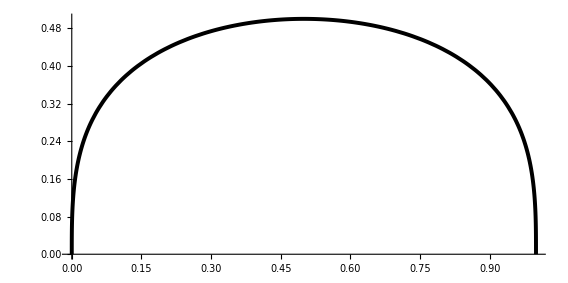

```mathematica
cl1=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),1/2 Sin[θ]},{θ,0,π},PlotStyle->{Black,Thickness[0.005]}];
cl2=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),1.1/2 Sin[θ]},{θ,0,π},PlotStyle->{Blue,Thickness[0.005]}];
cl3=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),1/2 Sin[θ]+0.02Sin[20(θ-1/2 Sin[2θ])]},{θ,0,π},PlotStyle->{Blue,Thickness[0.005]}];
p1=Show[cl1,PlotRange->All,AxesStyle->Directive[Black,FontFamily->"Times",24],
FrameStyle->Directive[FontFamily->"Times",20]]
p2=Show[cl1,cl2,PlotRange->All,AxesStyle->Directive[Black,FontFamily->"Times",24],
FrameStyle->Directive[FontFamily->"Times",20]];
p3=Show[cl1,cl3,PlotRange->All,AxesStyle->Directive[Black,FontFamily->"Times",24],
FrameStyle->Directive[FontFamily->"Times",20]];
```

```mathematica
RR=RandomReal[{-0.1,0.1},10]
```

{0.00685758,-0.061982,-0.0970546,0.054917,-0.0804495,-0.073151,-0.0590512,-0.0536919,-0.0626736,-0.0932286}

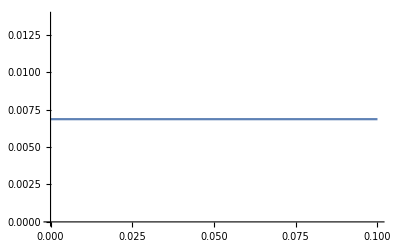

```mathematica
Plot[RR[[1]],{x,0.1(1-1),0.1}]
```

```mathematica
step[x_]=Piecewise[{RR[[#]],0.1(#-1)<x<0.1#}&/@Range@10]
```

Piecewise[{{0.00685758, 0.<x<0.1}, {-0.061982, 0.1<x<0.2}, {-0.0970546, 0.2<x<0.3}, {0.054917, 0.3<x<0.4}, {-0.0804495, 0.4<x<0.5}, {-0.073151, 0.5<x<0.6}, {-0.0590512, 0.6<x<0.7}, {-0.0536919, 0.7<x<0.8}, {-0.0626736, 0.8<x<0.9}, {-0.0932286, 0.9<x<1.}, {0, True}}]

```mathematica
cl1=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),1/2 Sin[θ]},{θ,0,π},PlotStyle->{Black,Thickness[0.005]}];
```

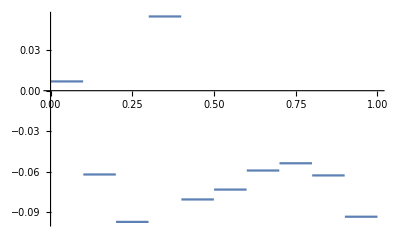

```mathematica
Pstep=Plot[step[x],{x,0,1}]
```

{0.00515694,0.0420559,0.0122262,0.0154811,-0.0354329,-0.0479834,0.0155627,0.00911609,0.0206986,-0.0396015,-0.013819,0.0336286,0.03901,-0.0465703,-0.020286,-0.0172238,0.0448072,-0.00781238,0.0214608,-0.00318878,-0.00534177,0.0387571,-0.0113008,0.0440545,0.0305005,0.0332197,0.0381255,-0.03147,-0.0441678,0.0415142,-0.0490863,-0.0150771,-0.0214598,0.000357314,-0.0373673,0.0496453,-0.00362896,-0.0295433,0.01037,-0.0347509,0.0359038,-0.0302098,-0.046391,-0.00586439,0.010761,0.0465801,0.0219527,-0.0449476,-0.00431383,-0.042181,0.021665,0.0480608,-0.00100814,0.0125597,0.0370919,-0.0478673,-0.0354659,-0.0498268,-0.00877383,-0.0153621,0.0193606,-0.0433845,0.0491754,0.0231344,-0.00757871,0.0292883,0.00461842,0.0355285,-0.020314,0.0104221,0.0105081,-0.0442956,-0.030125,0.0277583,0.0122578,-0.0236815,-0.017603,-0.0421761,0.0371345,-0.00933099,0.0341815,-0.0150269,-0.00631217,-0.015558,0.00687299,-0.0159245,0.0152384,-0.0141394,-0.0365959,-0.00859479,0.0344711,-0.0382973,0.0209841,-0.0496768,0.0274055,-0.00785375,-0.0402164,0.0036332,0.0109245,-0.0190995,-0.0327328,0.0343401}

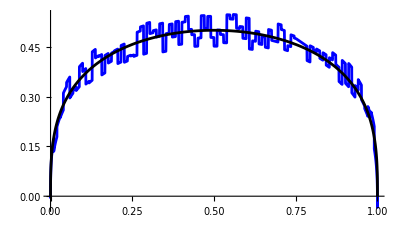

```mathematica
fre=100;
lim = 0.05;
RRow=RandomReal[{-lim,lim},fre];
RR = Join[{RandomReal[{0.0,lim}]},RRow,{RandomReal[{0.0,lim}]}]
Len = Length@RR;
int = 1/Len;
step[x_]=Piecewise[{RR[[#]],int(#-1)<x<int#}&/@Range@Len];
Ppert=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),1/2 Sin[θ]-step[1/π(θ-1/2 Sin[2θ])]},{θ,0,π},PlotStyle->{Blue,Thickness[0.005]}];
Ppert1=Show[Ppert,cl1]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Study/ASME2018/Figure

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Steps.pdf",Ppert1]
```

Steps.pdf

```mathematica
Export["self_similar.pdf",p2]
```

self_similar.pdf

```mathematica
Export["FixedVolume.pdf",p3]
```

FixedVolume.pdf

```mathematica
Series[Sin[θ],{θ,0,3}]
```

θ-θ^3/6+O[θ]^4

```mathematica
Series[θ-1/2 Sin[2θ],{θ,0,3}]
```

(2 θ^3)/3+O[θ]^4

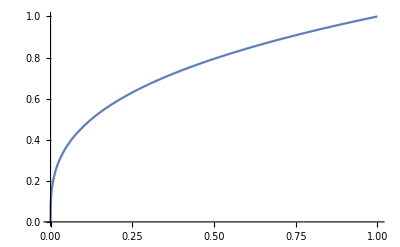

```mathematica
Plot[x^(1/3),{x,0,1}]
```

```mathematica
pclau=Plot[{-80x,80x},{x,0,0005},PlotStyle->Directive[{RGBColor[1,0,0],Thickness[0.008]}]];
```

```mathematica
pcons=Plot[{-97.97958971132712x,97.97958971132712x},{x,0,0007},PlotStyle->Directive[{RGBColor[0,0,1],Thickness[0.008]}]];
```

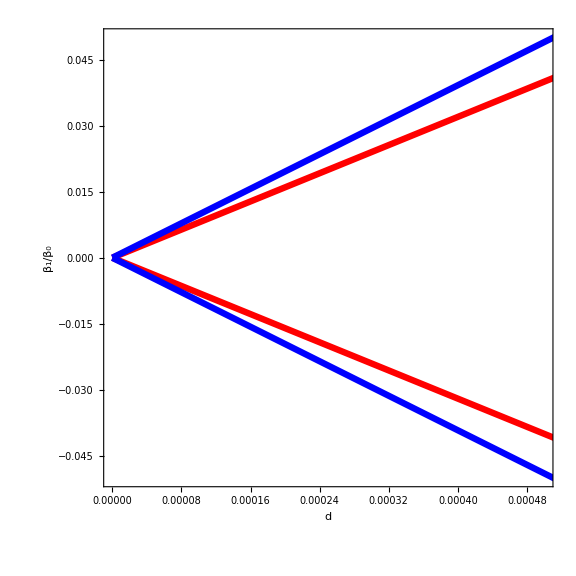

```mathematica
ppline=Show[pclau,pcons,PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0.5,0,0],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
AxesStyle->Directive[Black,FontFamily->"Times",24],
Frame->True,
FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Steps.pdf",ppline]
```

/Users/wenqiangfang/Dropbox (Brown)/Study/ASME2018/Figure

Steps.pdf